{a→25.6913}

25.6913 Cos[θ]^2

| Estimate | Standard Error | t-Statistic | P-Value
a | 25.6913 | 0.443688 | 57.904 | 5.03539×10^-15

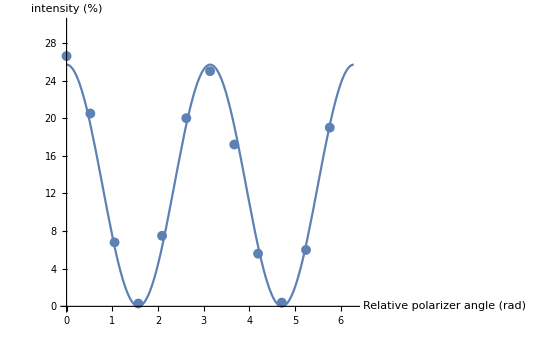

{b→1.99706}

1.99706 θ

| Estimate | Standard Error | t-Statistic | P-Value
b | 1.99706 | 0.0129945 | 153.684 | 2.21288×10^-10

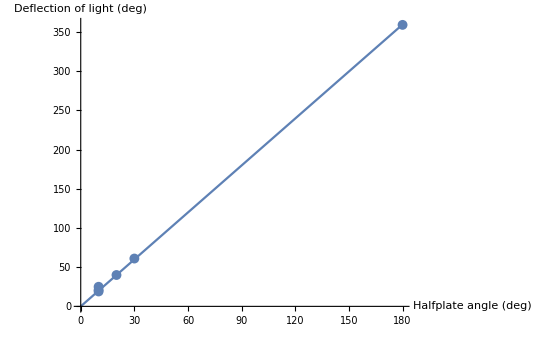

```mathematica
Clear[a,b,θ];

(* Data = Import["C:\Users\jprasadh\Downloads\Experiment 5\RelAngIntData.csv"] *)

RelAngIntData = {{0.,26.6},{0.52,20.5},{1.05,6.8},{1.57,0.3},{2.09,7.5},{2.62,20},{3.14,25},{3.67,17.2},{4.19,5.6},{4.71,0.4},{5.24,6},{5.76,19}};

HalfplatePolData = {{10,25},{20,40},{30,61},{10,19},{180,359},{10,21}};

FindFit[RelAngIntData,a (Cos[θ])^2,{a},θ]
intensity[θ_]=a (Cos[θ])^2/.%;
nlm=NonlinearModelFit[RelAngIntData,a (Cos[θ])^2,{a},θ];
Normal[nlm]
nlm["ParameterTable"]
Show[Plot[intensity[θ],{θ,0,2 Pi},PlotRange->{0,30}],ListPlot[RelAngIntData],AxesLabel->{"Relative polarizer angle (rad)","intensity (%)"}]

FindFit[HalfplatePolData,b θ,{b},θ]
newangle[θ_]=b θ/.%;
lm=NonlinearModelFit[HalfplatePolData,b θ,{b},θ];
Normal[lm]
lm["ParameterTable"]
Show[Plot[newangle[θ],{θ,0,180},PlotRange->{0,360}],ListPlot[HalfplatePolData],AxesLabel->{"Halfplate angle (deg)","Deflection of light (deg)"}]
```